{17.9667,11.,6.41667,22.,9.53333,18.15}

{3,5,4,5,7,6}

{2.24583,0.916667,0.641667,1.83333,0.595833,1.29643}

13.6905 % athlete profit

42.5333 $ Nceno profit

1.4321 % of user stake per user per week $ Nceno profit

4.72593 rev per user $ Nceno profit

0.787654 rev per user per week $ Nceno profit

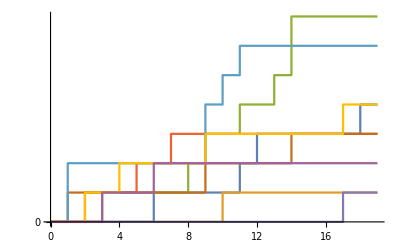

```mathematica
lambda = .1833;
chDur = 6;
sessions =3;
participants = 9;
ptns={{35,65,0,0,0,0,0,0,0,0,0,0},{23,11,28,38,0,0,0,0,0,0,0,0},{14,15,5,20,13,33,0,0,0,0,0,0},{9,14,7,4,15,13,11,27,0,0,0,0},{7,10,10,4,3,11,13,7,11,24,0,0},{6,8,10,6,2,3,9,12,8,6,12,18}};
stake = 55;

workout = Range[0,sessions chDur,1];
misses= Range[0,participants sessions chDur,1];
players = RandomFunction[PoissonProcess[ lambda],{0,chDur sessions,1},participants];
data = Normal[players];
counts = Table[data[[All,(s+1),2]]-data[[All,(s),2]],{s,1,sessions chDur}];
                 weeklySums = Table[Sum[(stake*0.01*ptns[[chDur/2,w]]/sessions) Sum[counts[[r,i]],{i,1,participants}],{r,(w-1)sessions + 1,w sessions}],{w,1,chDur}]
winnerCt =Table[0,chDur];
For[p=1,p<participants+1,p++,
For[w=1,w<chDur+1,w++,
If[Sum[counts[[r,p]],{r,(w-1)sessions + 1,w sessions}]==0,winnerCt[[w]]++];
]
]
                 winnerCt
athletePO = Table[0,chDur];
For[w=1,w<chDur+1,w++,
athletePO[[w]]= N[.5 weeklySums[[w]]/(1+winnerCt[[w]])]
]
                athletePO
100*(Sum[athletePO[[i]],{i,1,chDur}]/stake)"% athlete profit"

ncenoPO = Table[0,chDur];
For[w=1,w<chDur+1,w++,
ncenoPO[[w]]= .5 weeklySums[[w]]
]
ncenoProfit = Sum[ncenoPO[[i]],{i,1,chDur}] "$ Nceno profit"
100 ncenoProfit/(participants*stake*chDur) "% of user stake per user per week"
ncenoProfit/(participants) "rev per user"
ncenoProfit/(participants*chDur) "rev per user per week"

ListStepPlot[players,Filling->None,Ticks->{workout,misses}, PlotRange->{{0,chDur sessions+1},Automatic}]
MatrixForm[counts];
```